```mathematica
f[x_]:=1/5+25 x-200 x^2+675 x^3-900 x^4+400 x^5;
a=0;b=4/5;n=6;
h=(b-a)/n;
xnodes=Table[a+k h,{k,0,n}];
ynodes=f/@xnodes;
data=Transpose[{xnodes,ynodes}];
```

```mathematica
linear=Table[InterpolatingPolynomial[data[[i;;i+1]],x]//Simplify,{i,1,6}];

quad={InterpolatingPolynomial[data[[1;;3]],x]//Simplify,InterpolatingPolynomial[data[[3;;5]],x]//Simplify,InterpolatingPolynomial[data[[5;;7]],x]//Simplify};

cubic={InterpolatingPolynomial[data[[1;;4]],x]//Simplify,InterpolatingPolynomial[data[[4;;7]],x]//Simplify};

deg6={InterpolatingPolynomial[data[[1;;7]],x]//Simplify};
```

```mathematica
dropAll=Table[{Black,Thin,Line[{{xnodes[[k]],0},{xnodes[[k]],ynodes[[k]]}}]},{k,1,7}];

dropEvery2=Table[{Black,Thin,Line[{{xnodes[[k]],0},{xnodes[[k]],ynodes[[k]]}}]},{k,{1,3,5,7}}];

dropEvery3=Table[{Black,Thin,Line[{{xnodes[[k]],0},{xnodes[[k]],ynodes[[k]]}}]},{k,{1,4,7}}];

dropEvery7=Table[{Black,Thin,Line[{{xnodes[[k]],0},{xnodes[[k]],ynodes[[k]]}}]},{k,{1,7}}];
```

```mathematica
plot1=Plot[f[x],{x,0,4/5},PlotStyle->{Thick,Purple},PlotRange->{0,6},AxesLabel->{"x","f(x)"},PlotLabel->Style["1. Original function",Bold,14],Epilog->{Red,PointSize[Medium],Point[data]}];

plot2=Show[Plot[f[x],{x,0,4/5},PlotStyle->{Thick,Purple}],Table[Plot[linear[[i]],{x,xnodes[[i]],xnodes[[i+1]]},PlotStyle->{Green,Thick}],{i,1,6}],PlotRange->{0,6},AxesLabel->{"x","f(x)"},PlotLabel->Style["2. Function + 6 linear pieces\n(Trapezoidal)",Bold,14],Epilog->{Red,PointSize[Medium],Point[data],dropAll                                      (*<<<all 7 vertical lines*)}];

plot3=Show[Plot[f[x],{x,0,4/5},PlotStyle->{Thick,Purple}],Plot[quad[[1]],{x,xnodes[[1]],xnodes[[3]]},PlotStyle->{Green,Thick}],Plot[quad[[2]],{x,xnodes[[3]],xnodes[[5]]},PlotStyle->{Green,Thick}],Plot[quad[[3]],{x,xnodes[[5]],xnodes[[7]]},PlotStyle->{Green,Thick}],PlotRange->{0,6},AxesLabel->{"x","f(x)"},PlotLabel->Style["3. Function + 3 quadratics\n(Simpson's 1/3)",Bold,14],Epilog->{Red,PointSize[Medium],Point[data],dropEvery2                                   (*<<<only at 0,2h,4h,6h*)}];

plot4=Show[Plot[f[x],{x,0,4/5},PlotStyle->{Thick,Purple}],Plot[cubic[[1]],{x,xnodes[[1]],xnodes[[4]]},PlotStyle->{Green,Thick}],Plot[cubic[[2]],{x,xnodes[[4]],xnodes[[7]]},PlotStyle->{Green,Thick}],PlotRange->{0,6},AxesLabel->{"x","f(x)"},PlotLabel->Style["4. Function + 2 cubics\n(Simpson's 3/8)",Bold,14],Epilog->{Red,PointSize[Medium],Point[data],dropEvery3                                   (*<<<only at 0,3h,6h*)}];

plot5=Show[ Plot[f[x],{x,0,4/5},PlotStyle->{Thick,Purple}],Plot[f[x],{x,0,4/5},PlotStyle->{Thick,Purple}],Plot[deg6[[1]],{x,xnodes[[1]],xnodes[[7]]},PlotStyle->{Green,Thick}],PlotRange->{0,6},AxesLabel->{"x","f(x)"},PlotLabel->Style["Function + Degree 6 interpolation",Bold,14],Epilog->{Red,PointSize[Medium],Point[data], dropEvery7 ,ImageSize->900 }];
```

```mathematica
Column[{"Equations for plot-2:",TableForm[Table[{"l"<>ToString[i]<>"(x) =",linear[[i]]},{i,6}]],"Equations for plot-3:",TableForm[Table[{"p"<>ToString[i]<>"(x) =",quad[[i]]},{i,3}]],"Equations for plot-4:",TableForm[Table[{"c"<>ToString[i]<>"(x) =",cubic[[i]]},{i,2}]],"Equations for plot-5:",TableForm[Table[{"c"<>ToString[i]<>"(x) =",deg6[[i]]},{i,1}]]}]
```

Equations for plot-2:
l1(x) = | 1/5+(16861 x)/2025
l2(x) = | (2405+1861 x)/2025
l3(x) = | (-1243+15541 x)/2025
l4(x) = | (-1291+15661 x)/2025
l5(x) = | (12021-9299 x)/2025
l6(x) = | (32581-40139 x)/2025
Equations for plot-3:
p1(x) = | 1/5+(24361 x)/2025-(250 x^2)/9
p2(x) = | (-1195+15241 x+450 x^2)/2025
p3(x) = | (-29099+129481 x-115650 x^2)/2025
Equations for plot-4:
c1(x) = | 1/225 (45+3769 x-18200 x^2+29875 x^3)
c2(x) = | 1/225 (-1491+6329 x-600 x^2-6125 x^3)
Equations for plot-5:
c1(x) = | 1/5+25 x-200 x^2+675 x^3-900 x^4+400 x^5

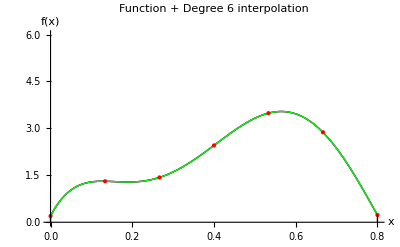

interpolation-figure-deg6.pdf

```mathematica
plot5
Export["interpolation-figure-deg6.pdf",plot5]
```

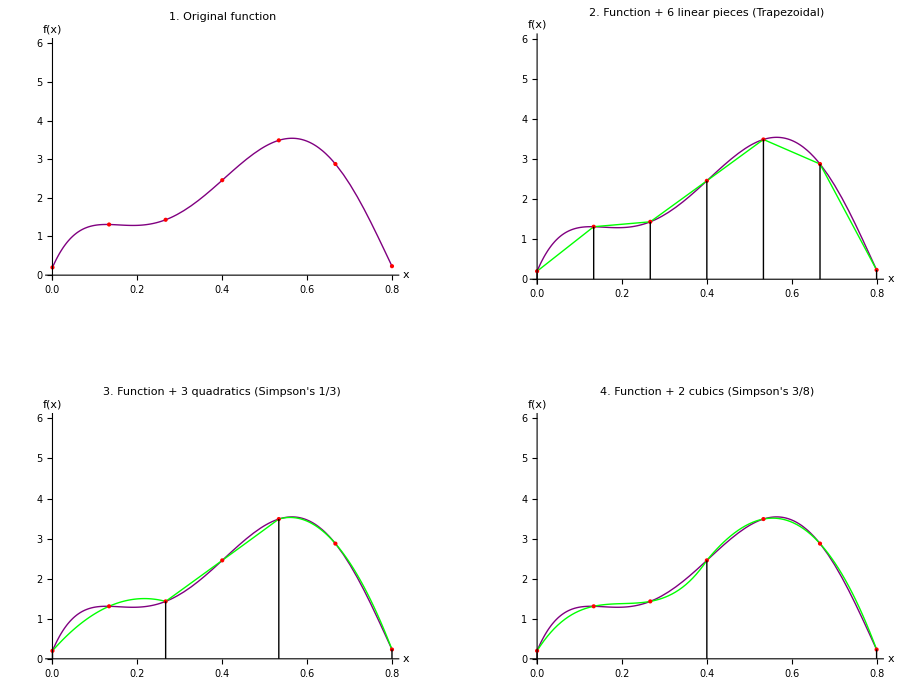

interpolations-figure-fun-deg1-deg2-deg3.pdf

```mathematica
imgfig=GraphicsGrid[{{plot1,plot2},{plot3,plot4}},ImageSize->900,Spacings->{60,60}]
Export["interpolations-figure-fun-deg1-deg2-deg3.pdf",imgfig]
```